### Learning Rate

#### epochs : 10, L2N : 350, L3N : 350, BS : 64

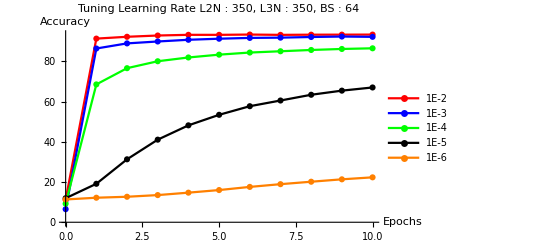

```mathematica
x= {0,1,2,3,4,5,6,7,8,9,10};
y1 = {11.21,91.34,92.25,92.88,93.22,93.21,93.36,93.2,93.29,93.31,93.34}; (*1e-02*)
y2 = {6.5,86.42,88.96,89.91,90.76,91.29,91.69,91.82,92.14,92.37,92.22}; (*1e-03*)
y3 = {9.24,68.56,76.63,80.08,81.96,83.36,84.41,85.05,85.69,86.19,86.52}; (*1e-04*)
y4 = {11.95,19.13,31.31,41.08,48.2,53.44,57.72,60.55,63.41,65.46,67.04}; (*1e-05*)
y5 = {11.34,12.2,12.68,13.51,14.72,16.01,17.58,18.94,20.16,21.35,22.34}; (*1e-06*)

P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->All,
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Learning Rate
L2N : 350, L3N : 350, BS : 64",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"1E-2"],P[y2,Blue,"1E-3"],P[y3,Green,"1E-4"],P[y4,Black,"1E-5"],P[y5, Orange,"1E-6"]]
```

### Node Count

#### Initial Plot

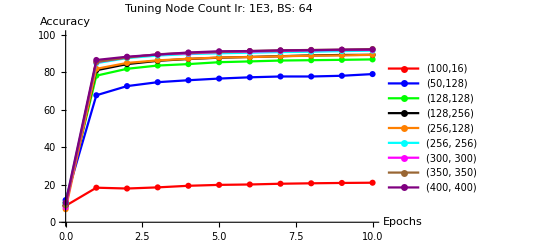

```mathematica
x= {0,1,2,3,4,5,6,7,8,9,10};
y1={8.78,18.41,17.97,18.58,19.43,19.91,20.12,20.52,20.75,20.94,21.06}; (*100, 16*)
y2={11.81,67.65,72.53,74.62,75.66,76.55,77.22,77.66,77.65,78.04,78.94}; (*50, 128*)
y3={10.34,78.09,81.75,83.49,84.26,85.27,85.69,86.15,86.34,86.53,86.76}; (*128, 128*)
y4={8.89,80.98,84.26,86.01,86.99,87.67,88.06,88.47,88.87,89.12,89.19}; (*128, 256*)
y5={6.95,81.73,84.88,86.25,87.09,87.77,87.98,88.42,88.73,88.88,89.18}; (*256, 128*)
y6={10.19,84.76,87.47,88.81,89.62,90.01,90.34,90.66,90.84,91.17,91.42}; (*256, 256*)
y7={7.98,85.28,87.89,89.44,89.91,90.64,90.92,91.24,91.62,91.77,91.84}; (*300, 300*)
y8={8.96,85.4,87.73,89.5,90.21,90.76,91.2,91.55,91.8,91.93,92.28}; (*350, 350*)
y9={10.48,86.45,88.19,89.34,90.44,91.09,91.21,91.58,91.69,91.95,92.08}; (*400, 400*)

P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->{0,100},
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Node Count
lr: 1E3, BS: 64",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"(100,16)"],P[y2,Blue,"(50,128)"],P[y3,Green,"(128,128)"],P[y4,Black,"(128,256)"],P[y5, Orange,"(256,128)"],
P[y6, Cyan,"(256, 256)"],P[y7, Magenta,"(300, 300)"], P[y8, Brown,"(350, 350)"], P[y9, Purple,"(400, 400)"]]
```

#### Changing Range

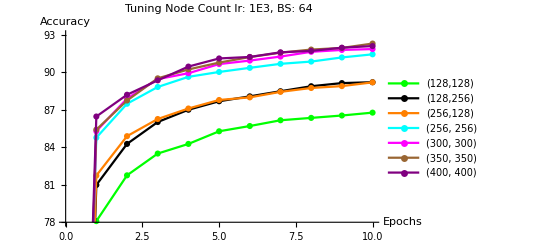

```mathematica
P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->{78,93},
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Node Count
lr: 1E3, BS: 64",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y3,Green,"(128,128)"],P[y4,Black,"(128,256)"],P[y5, Orange,"(256,128)"],
P[y6, Cyan,"(256, 256)"],P[y7, Magenta,"(300, 300)"], P[y8, Brown,"(350, 350)"], P[y9, Purple,"(400, 400)"]]
```

### Epochs

#### Initial Plot epochs : 50, η : 0.001, L2N : 350, L3N : 350, BS : 64

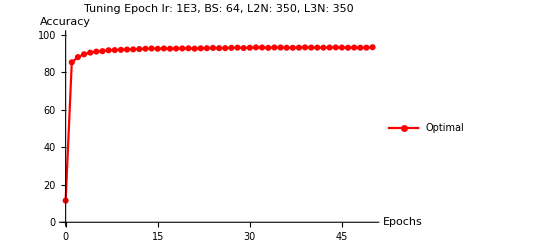

```mathematica
x = Range[51]-1;
y1 ={11.53,85.22,87.99,89.5,90.37,90.91,91.15,91.62,91.72,91.85,92.01,92.11,92.27,92.43,92.58,92.43,92.6,92.46,92.55,92.62,92.68,92.48,92.66,92.73,92.89,92.75,92.75,92.93,93.03,92.8,92.97,93.16,93.11,92.91,93.11,93.09,92.97,92.94,93.02,93.16,93.07,93.05,93.02,93.09,93.14,93.09,92.97,93.07,92.99,93.02,93.24};

P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->{0,100},
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Epoch
lr: 1E3, BS: 64, L2N: 350, L3N: 350",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"Optimal"]]
```

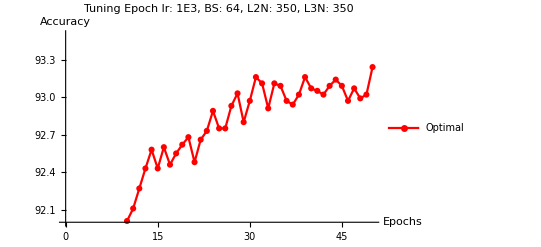

```mathematica
P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->{92,93.5},
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Epoch
lr: 1E3, BS: 64, L2N: 350, L3N: 350",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"Optimal"]]
```

### Batch Size

```mathematica
x= {5,10,15,30,60,100,300};
y1={0}; (*5*)
y2={0}; (*10*)
y3={0}; (*15*)
y4={0}; (*30*)
y5={0}; (*60*)
y6={0}; (*100*)
y7={0}; (*300*)

P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->All,
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Tuning Batch Size
lr: 1E-3, L2N : 350, L3N : 350",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"1E-2"]]
```

### ReLU vs . Sigmoid

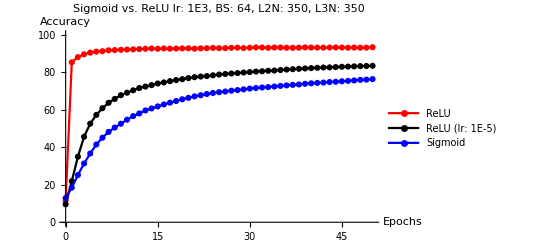

```mathematica
x = Range[51]-1;
y1 ={11.53,85.22,87.99,89.5,90.37,90.91,91.15,91.62,91.72,91.85,92.01,92.11,92.27,92.43,92.58,92.43,92.6,92.46,92.55,92.62,92.68,92.48,92.66,92.73,92.89,92.75,92.75,92.93,93.03,92.8,92.97,93.16,93.11,92.91,93.11,93.09,92.97,92.94,93.02,93.16,93.07,93.05,93.02,93.09,93.14,93.09,92.97,93.07,92.99,93.02,93.24}; (*ReLU*)
y2={12.9,18.45,25.16,31.29,36.62,41.42,45.05,48.14,50.46,52.47,54.65,56.53,57.97,59.56,60.62,61.72,62.78,63.69,64.6,65.52,66.27,67.05,67.67,68.32,68.86,69.3,69.64,70.08,70.42,70.8,71.2,71.51,71.79,72.01,72.31,72.63,72.9,73.18,73.41,73.76,74.02,74.25,74.42,74.7,74.85,75.1,75.31,75.56,75.84,75.99,76.26}; (*Sigmoid*)
y3={9.54,21.88,34.93,45.55,52.53,57.19,60.78,63.64,65.7,67.69,69.02,70.28,71.5,72.29,73.06,73.93,74.5,75.16,75.76,76.23,76.8,77.29,77.64,77.88,78.29,78.68,78.97,79.24,79.47,79.77,80.01,80.27,80.46,80.71,80.83,81.1,81.35,81.54,81.75,81.94,82.11,82.29,82.45,82.51,82.67,82.83,82.92,83.04,83.18,83.25,83.35}; (*ReLU lr = 1E-5*)

P[y_,color_,label_]:=ListPlot[Transpose[{x,y}],Joined->True,PlotRange->{0,100},
PlotMarkers-> Automatic,PlotStyle->color,PlotLegends->{label}, 
PlotLabel->"Sigmoid vs. ReLU
lr: 1E3, BS: 64, L2N: 350, L3N: 350",
AxesLabel->{"Epochs","Accuracy"}]

Show[P[y1,Red,"ReLU"],P[y3,Black,"ReLU (lr: 1E-5)"],P[y2,Blue,"Sigmoid"]]
```